# Setup

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Miguel\Github\Entropy\second_run_desktop

```mathematica
Get["C:\\Users\\Miguel\\Github\\Entropy\\QMB_offline.wl"]
```

```mathematica
LaunchKernels[14]
```

{Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14)}

```mathematica
Needs["MaTeX`"];
```

MaTeX::shdw: Symbol MaTeX appears in multiple contexts {MaTeX`,Notebook$$32$246434`}; definitions in context MaTeX` may shadow or be shadowed by other definitions.

# Eigenvectors analysis

```mathematica
Clear[VNentropy];
VNentropy[0|0.]=0;
VNentropy[x_]:=-x*Log[x];
(*Clear[svn];
svn[L_,La_,Lb_,ini_,eigenval_,eigenvec_,t_]:=Module[{state=StateEvolution[t,ini,eigenval,eigenvec],rho,λ,purity,dim=2^L,dima=2^(L-La),dimb=2^(L-Lb)},
rho=MatrixPartialTrace[Dyad[state],1,{dima,dimb}];
purity=Chop[Tr[rho.rho]];
λ=Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho]]]]];
{Chop[λ],1-purity}
];
Clear[sdiag];
sdiag[ini_]:=Module[{state=Dyad[Conjugate[eigenvec].ini],rho,λ},
rho=MatrixPartialTrace[state,1,{2^(L/2),2^(L/2)}];
λ=Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho]]]]]
];*)
Clear[svn];
svn[L_,La_,Lb_,ini_,eigenval_,eigenvec_,t_]:=Module[{state=StateEvolution[t,ini,eigenval,eigenvec],rho,λ,purity,dima=2^(L-La),dimb=2^(L-Lb)},
rho=MatrixPartialTrace[Dyad[state],1,{dima,dimb}];
Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho]]]]]
];
Clear[sdiag];
sdiag[L_,La_,Lb_,ini_]:=Module[{state=Dyad[ini],dima=2^(L-La),dimb=2^(L-Lb),rho},
rho=MatrixPartialTrace[state,1,{dima,dimb}];
Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho]]]]]
];
(*Define the Pauli matrices*)
Clear[sx,sy,sz];
sx={{0,1},{1,0}};
sy={{0,-I},{I,0}};
sz={{1,0},{0,-1}};
(*Define collective spin operators for n spins*)
Clear[Jx,Jy,Jz];
Jx[n_]:=SparseArray[(1/2)Sum[KroneckerProduct@@Table[If[j==i,sx,IdentityMatrix[2]],{j,n}],{i,n}]];
Jy[n_]:=SparseArray[(1/2)Sum[KroneckerProduct@@Table[If[j==i,sy,IdentityMatrix[2]],{j,n}],{i,n}]];
Jz[n_]:=SparseArray[(1/2)Sum[KroneckerProduct@@Table[If[j==i,sz,IdentityMatrix[2]],{j,n}],{i,n}]];
Jza[L_,La_]:=SparseArray[(1/2)Sum[KroneckerProduct@@Table[If[j==i,sz,IdentityMatrix[2]],{j,L}],{i,La}]];
```

```mathematica
L=6;
g=J=1;
h=1.0;
H=IsingNNOpenHamiltonian[h,g,J,L];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];
```

```mathematica
La=3;
Lb=L-La;
ipreigenvec=ParallelTable[Total[Abs[i]^4],{i,eigenvec}];
entropies=ParallelTable[sdiag[L,La,Lb,i],{i,eigenvec},DistributedContexts->Full];
```

```mathematica
data=Table[{{eigenval[[i]],entropies[[i]]}},{i,Length[eigenvec]}];
```

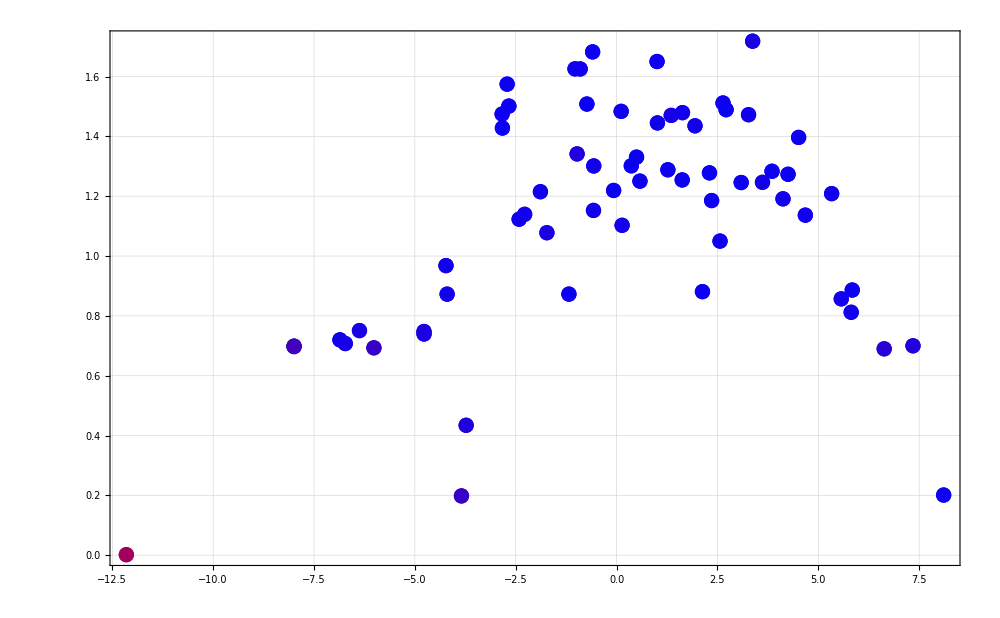

```mathematica
colors=Table[Blend[{Blue,Red},i],{i,ipreigenvec}];
custom[x_]:=Blend[{Blue,Red},x];
plot=ListPlot[data,PlotStyle->colors,PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style[MaTeX["h = "<>ToString[h]<>" \\,, L="<>ToString[L]<>",\\, L_{a}="<>ToString[La]<>",\\, L_{b}="<>ToString[Lb]<>",\\,|E_{i}\\rangle",FontSize->35],Black],FrameLabel->{Style[MaTeX["E",FontSize->35],Black],Style[MaTeX["S_{vn}",FontSize->35],Black]},ImageSize->1000,PlotLegends->BarLegend[{custom,{Min[ipreigenvec],Max[ipreigenvec]}},LegendLabel->Style[MaTeX["IPR_{\\{0,1\\}}",FontSize->25],Black]]]
(*Export["svneigenvecs_L_"<>ToString[L]<>"_La_"<>ToString[La]<>"_h_"<>ToString[h]<>"_.png",plot,ImageResolution->300];*)
```

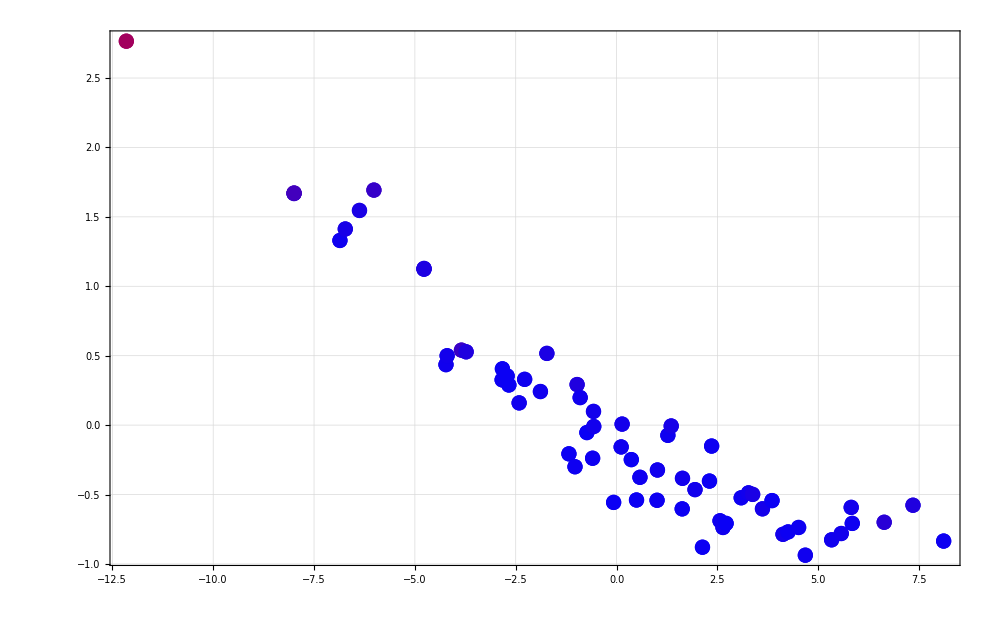

```mathematica
jzs=ParallelTable[Chop[ConjugateTranspose[i].Jza[L,L].i],{i,eigenvec},DistributedContexts->Full];
data=Table[{{eigenval[[i]],jzs[[i]]}},{i,Length[eigenvec]}];
plot=ListPlot[data,PlotStyle->colors,PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style[MaTeX["h = "<>ToString[h]<>" \\,, L="<>ToString[L]<>",\\, L_{a}="<>ToString[La]<>",\\, L_{b}="<>ToString[Lb]<>",\\,|E_{i}\\rangle",FontSize->35],Black],FrameLabel->{Style[MaTeX["E",FontSize->35],Black],Style[MaTeX["J_{z}",FontSize->35],Black]},ImageSize->1000,PlotLegends->BarLegend[{custom,{Min[ipreigenvec],Max[ipreigenvec]}},LegendLabel->Style[MaTeX["IPR_{\\{0,1\\}}",FontSize->25],Black]]]
(*Export["svneigenvecs_L_"<>ToString[L]<>"_La_"<>ToString[La]<>"_h_"<>ToString[h]<>"_.png",plot,ImageResolution->300];*)
```

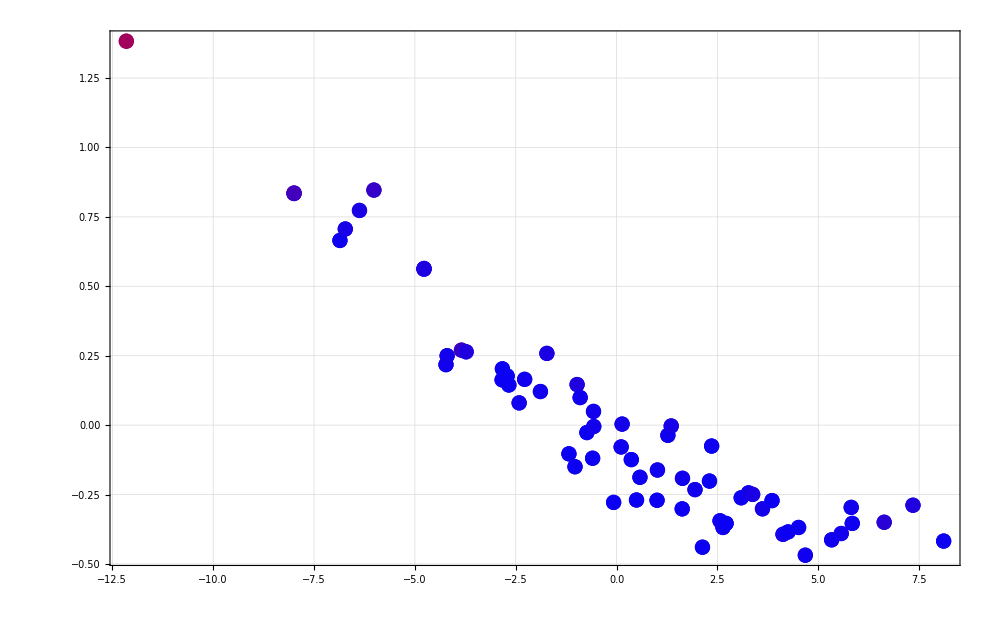

```mathematica
(*Magnetization in partition A*)
jzs=ParallelTable[Chop[ConjugateTranspose[i].Jza[L,La].i],{i,eigenvec},DistributedContexts->Full];
data=Table[{{eigenval[[i]],jzs[[i]]}},{i,Length[eigenvec]}];
plot=ListPlot[data,PlotStyle->colors,PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style[MaTeX["h = "<>ToString[h]<>" \\,, L="<>ToString[L]<>",\\, L_{a}="<>ToString[La]<>",\\, L_{b}="<>ToString[Lb]<>",\\,|E_{i}\\rangle",FontSize->35],Black],FrameLabel->{Style[MaTeX["E",FontSize->35],Black],Style[MaTeX["J_{z_{a}}",FontSize->35],Black]},ImageSize->1000,PlotLegends->BarLegend[{custom,{Min[ipreigenvec],Max[ipreigenvec]}},LegendLabel->Style[MaTeX["IPR_{\\{0,1\\}}",FontSize->25],Black]]]
```

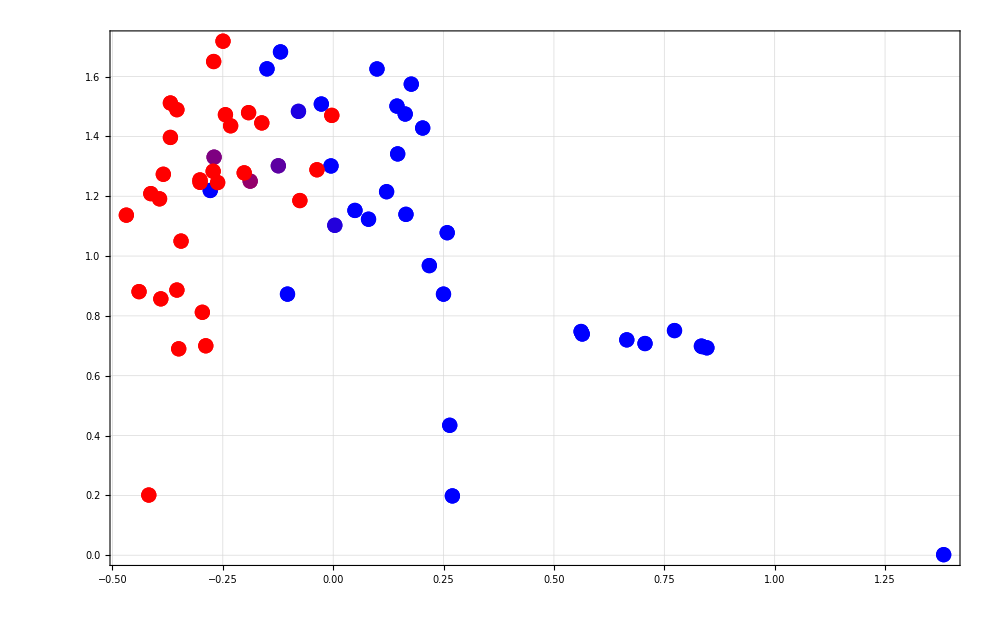

```mathematica
colors=Table[Blend[{Blue,Red},i],{i,eigenval}];
custom[x_]:=Blend[{Blue,Red},x];
data=Table[{{jzs[[i]],entropies[[i]]}},{i,Length[eigenvec]}];
plot=ListPlot[data,PlotStyle->colors,PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style[MaTeX["h = "<>ToString[h]<>" \\,, L="<>ToString[L]<>",\\, L_{a}="<>ToString[La]<>",\\, L_{b}="<>ToString[Lb]<>",\\,|E_{i}\\rangle",FontSize->35],Black],FrameLabel->{Style[MaTeX["J_{z}",FontSize->35],Black],Style[MaTeX["S_{vn}",FontSize->35],Black]},ImageSize->1000,PlotLegends->BarLegend[{custom,{Min[eigenval],Max[eigenval]}},LegendLabel->Style[MaTeX["E_{i}",FontSize->25],Black]]]
```

# Averages comparison

```mathematica
Clear[VNentropy];
VNentropy[0|0.]=0;
VNentropy[x_]:=-x*Log[x];
Clear[sdiag];
sdiag[L_,La_,Lb_,ini_]:=Module[{state=Dyad[ini],dima=2^(L-La),dimb=2^(L-Lb),rho},
rho=MatrixPartialTrace[state,1,{dima,dimb}];
Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho]]]]]
];

Clear[svn];
svn[L_,La_,Lb_,ini_,eigenval_,eigenvec_,t_]:=Module[{state=StateEvolution[t,ini,eigenval,eigenvec],rho,λ,purity,dima=2^(L-La),dimb=2^(L-Lb),vn},
rho=MatrixPartialTrace[Dyad[state],1,{dima,dimb}];
purity=Tr[rho.rho];
vn=Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho]]]]];
{Chop[vn],Chop[purity]}
];
Clear[Q];
Q[L_,La_,Lb_,eigenvec_,i_,j_]:=Q[L,La,Lb,eigenvec,i,j]=If[i<=j,Module[{projec=Dyad[eigenvec[[i]],eigenvec[[j]]],dima=2^(L-La),dimb=2^(L-Lb)},SparseArray[MatrixPartialTrace[projec,1,{dima,dimb}]]],ConjugateTranspose[Q[L,La,Lb,eigenvec,j,i]]];

Clear[meanpurity];
meanpurity[L_,La_,Lb_,ini_,eigenvec_]:=Module[{state=Conjugate[eigenvec].ini,dima=2^(L-La),dimb=2^(L-Lb),rho},
-Sum[(Abs[state[[i]]]^2)(Abs[state[[j]]]^2)Chop[Tr[Q[L,La,Lb,eigenvec,i,i].Q[L,La,Lb,eigenvec,j,j]]],{i,dima},{j,dima}]-Sum[(Abs[state[[i]]]^2)(Abs[state[[j]]]^2)Chop[Tr[Q[L,La,Lb,eigenvec,i,j].Q[L,La,Lb,eigenvec,j,i]]],{i,dima},{j,dima}]
];
```

```mathematica
L=6;
g=J=1;
h=1.0;
H=IsingNNOpenHamiltonian[h,g,J,L];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];
scaledeigenval=Rescale[eigenval+Abs[eigenval[[1]]]];
colors=Table[Blend[{Blue,Red},i],{i,scaledeigenval}];
custom[x_]:=Blend[{Blue,Red},x];
```

```mathematica
randoms=Table[RandomChainProductState[L],{i,1000}];
```

```mathematica
iprs=ParallelTable[Total[Abs[Conjugate[eigenvec].i]^4],{i,randoms}];
energies=ParallelTable[Chop[Conjugate[i].H.i],{i,randoms},DistributedContexts->Full];
stdenergies=ParallelTable[Chop[Conjugate[i].(H.H).i],{i,randoms},DistributedContexts->Full];
varenergies=Table[Sqrt[stdenergies[[i]]-energies[[i]]^2],{i,Length[energies]}];
```

```mathematica
La=3;
Lb=L-La;
entropydiag=ParallelTable[sdiag[L,La,Lb,Conjugate[eigenvec].i],{i,randoms},DistributedContexts->Full];
```

```mathematica
colors2=Table[Blend[{Blue,Red},i],{i,iprs}];
info=Table[{{energies[[i]],entropydiag[[i]]}},{i,Length[randoms]}];
ListPlot[info,PlotStyle->colors2,PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style[MaTeX["h = "<>ToString[h]<>" \\,, L="<>ToString[L]<>",\\, Random\\, product\\, states",FontSize->35],Black],FrameLabel->{Style[MaTeX["E",FontSize->35],Black],Style[MaTeX["S_{d}",FontSize->35],Black]},ImageSize->800,PlotRange->All,PlotLegends->BarLegend[{custom,{Min[iprs],Max[iprs]}},LegendLabel->MaTeX["IPR_{|E_{i}\\rangle}",FontSize->35]]]
```

-Graphics-

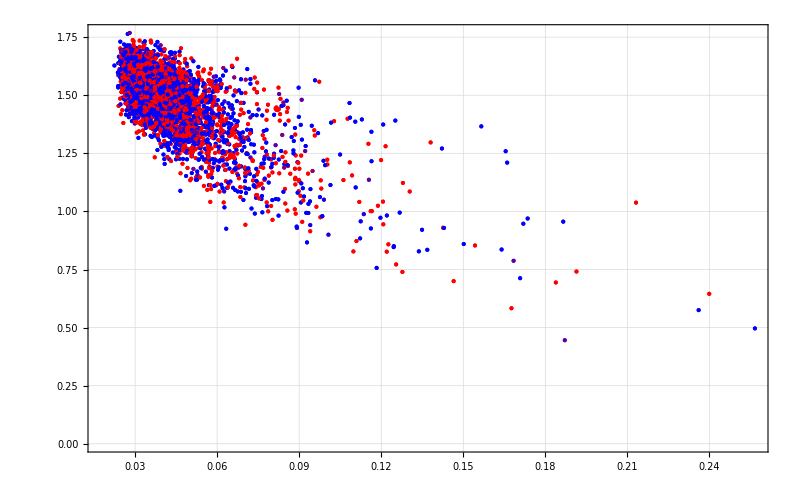

```mathematica
colors2=Table[Blend[{Blue,Red},i],{i,eigenval}];
info=Table[{{iprs[[i]],entropydiag[[i]]}},{i,Length[randoms]}];
ListPlot[info,PlotStyle->colors2,PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style[MaTeX["h = "<>ToString[h]<>" \\,, L="<>ToString[L]<>",\\, Random\\, product\\, states",FontSize->35],Black],FrameLabel->{Style[MaTeX["IPR_{E_i}",FontSize->35],Black],Style[MaTeX["S_{d}",FontSize->35],Black]},ImageSize->800,PlotRange->All,PlotLegends->BarLegend[{custom,{Min[eigenval],Max[eigenval]}},LegendLabel->MaTeX["E",FontSize->35]]]
```

```mathematica
meanpur=ParallelTable[1+meanpurity[L,La,Lb,i,eigenvec],{i,randoms}];
```

```mathematica
colors2=Table[Blend[{Blue,Red},i],{i,iprs}];
info=Table[{{energies[[i]],meanpur[[i]]}},{i,Length[randoms]}];
ListPlot[info,PlotStyle->colors2,PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style[MaTeX["h = "<>ToString[h]<>" \\,, L="<>ToString[L]<>",\\, Random\\, product\\, states",FontSize->35],Black],FrameLabel->{Style[MaTeX["E",FontSize->35],Black],Style[MaTeX["\\langle S_{2}\\rangle",FontSize->35],Black]},ImageSize->800,PlotRange->All,PlotLegends->BarLegend[{custom,{Min[iprs],Max[iprs]}},LegendLabel->MaTeX["IPR_{|E_{i}\\rangle}",FontSize->35]]]
```

-Graphics-

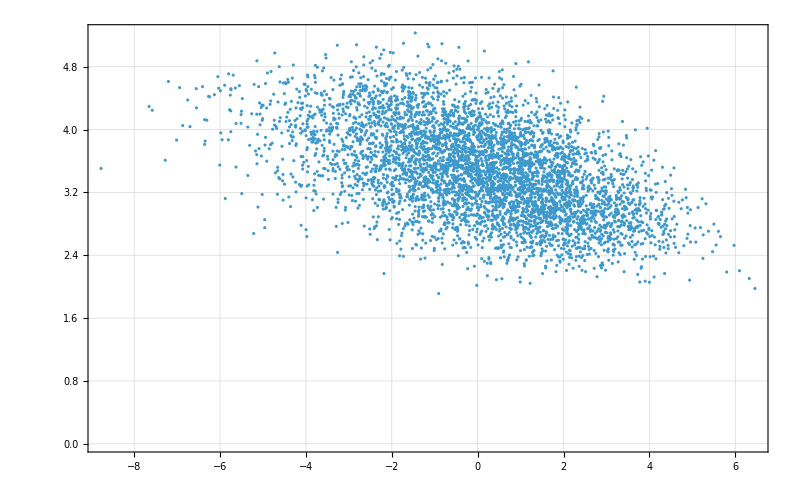

```mathematica
ListPlot[Transpose[{energies,varenergies}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style[MaTeX["h = "<>ToString[h]<>" \\,, L="<>ToString[L]<>",\\, Random\\, product\\, states",FontSize->35],Black],FrameLabel->{Style[MaTeX["E",FontSize->35],Black],Style[MaTeX["\\sigma_{E}",FontSize->35],Black]},ImageSize->800,PlotRange->All]
```

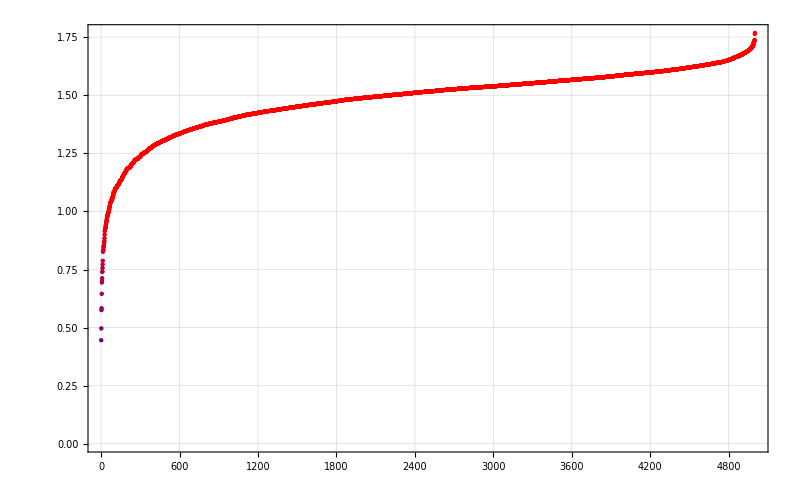

```mathematica
colors2=Table[Blend[{Blue,Red},i],{i,Sort[entropydiag]}];
sorted=Sort[entropydiag];
info=Table[{{i,sorted[[i]]}},{i,Length[Sort[entropydiag]]}];
ListPlot[info,PlotStyle->colors2,PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style[MaTeX["h = "<>ToString[h]<>" \\,, L="<>ToString[L]<>",\\, Random\\, product\\, states",FontSize->35],Black],FrameLabel->{Style[MaTeX["i",FontSize->35],Black],Style[MaTeX["S_{d}",FontSize->35],Black]},ImageSize->800,PlotRange->All,PlotLegends->BarLegend[{custom,{Min[Sort[entropydiag]],Max[Sort[entropydiag]]}},LegendLabel->MaTeX["S_{d}",FontSize->35]]]
```

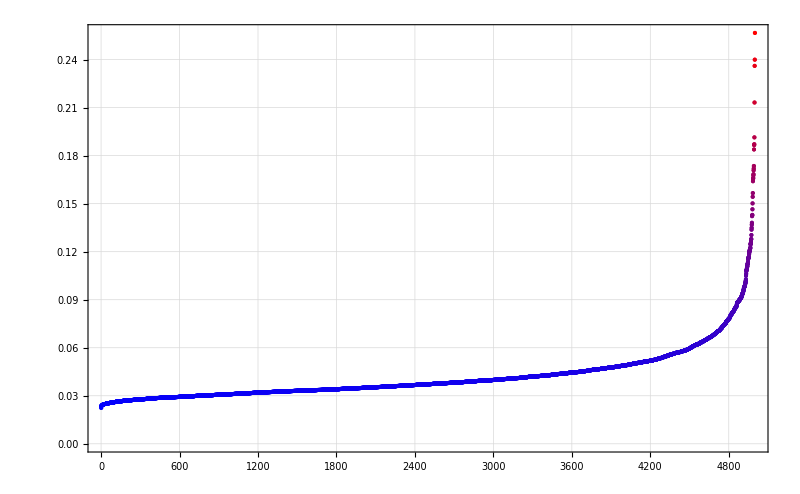

```mathematica
colors2=Table[Blend[{Blue,Red},i],{i,Rescale[Sort[iprs]]}];
sorted=Sort[iprs];
info=Table[{{i,sorted[[i]]}},{i,Length[Sort[iprs]]}];
ListPlot[info,PlotStyle->colors2,PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style[MaTeX["h = "<>ToString[h]<>" \\,, L="<>ToString[L]<>",\\, Random\\, product\\, states",FontSize->35],Black],FrameLabel->{Style[MaTeX["i",FontSize->35],Black],Style[MaTeX["IPR",FontSize->35],Black]},ImageSize->800,PlotRange->All,PlotLegends->BarLegend[{custom,{Min[Rescale[Sort[iprs]]],Max[Rescale[Sort[iprs]]]}},LegendLabel->MaTeX["IPR_{E_i}",FontSize->35]]]
```

```mathematica
difs=Outer[Subtract,eigenval,eigenval];
maxdif=Max[Abs[difs]];
Δt=1/(4*maxdif);
tf=10000;
tlist=Range[0,tf,Δt];
```

```mathematica
tlist//Length
```

810437

```mathematica
Length[tlist]/5000.
```

162.087

```mathematica
sortedrandoms=SortBy[Transpose[{Chop[iprs],randoms}],First];
```

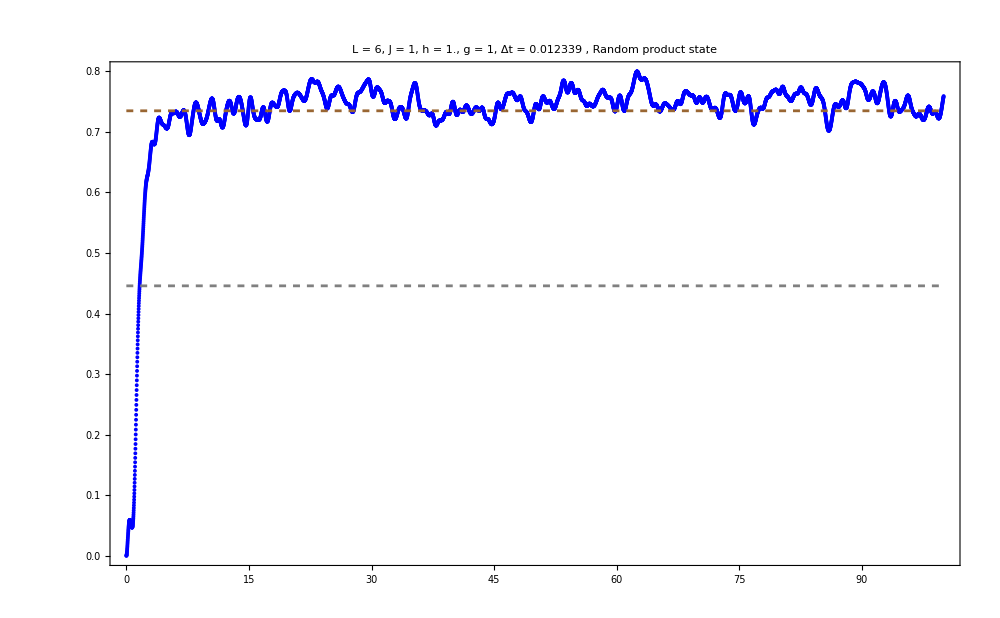

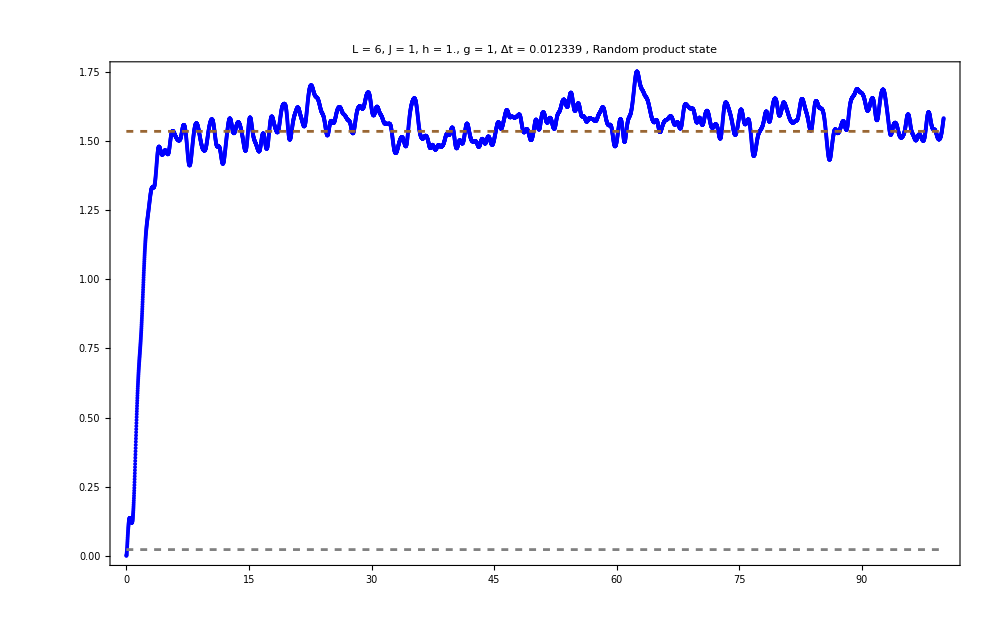

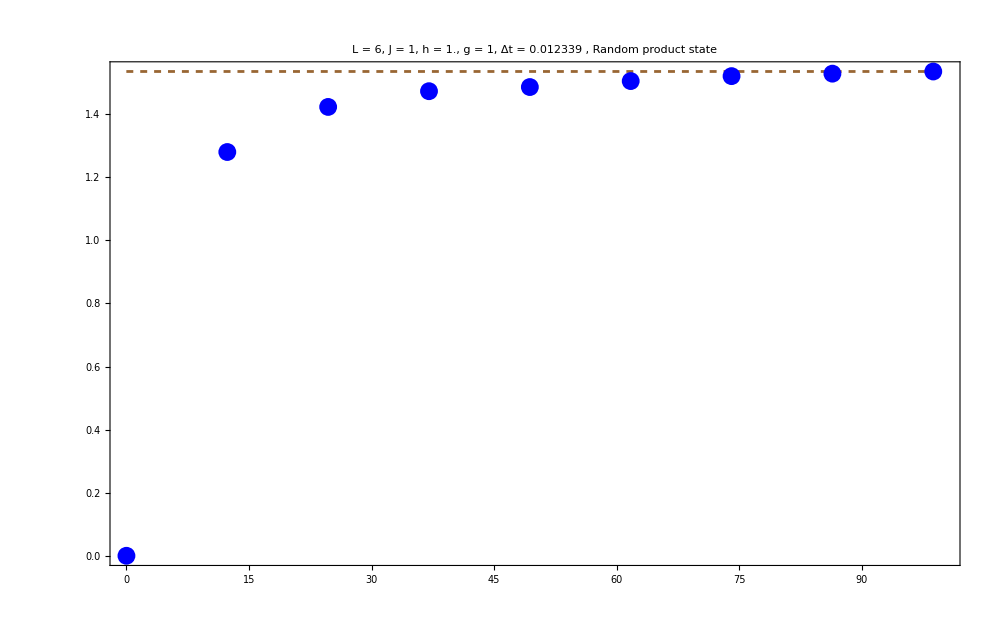

```mathematica
q=1;
ini=sortedrandoms[[q,2]];
entropies=ParallelTable[svn[L,La,Lb,ini,eigenval,eigenvec,t],{t,tlist},DistributedContexts->Full];
entro1=Transpose[{tlist,entropies[[All,1]]}];
entro2=Transpose[{tlist,1-entropies[[All,2]]}];
sortedpurities=SortBy[Transpose[{Chop[entropydiag],meanpur}],First];
fInterp = Interpolation[entro2]; 
 mean=NIntegrate[fInterp[t],{t,tlist[[1]],tlist[[-1]]}]/tlist[[-1]];
slplots=Show[{ListPlot[entro2,PlotStyle->colors2[[q]],PlotTheme->"Detailed",Joined->False,Axes->True,GridLines->None,PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = "<>ToString[h]<>", g = "<>ToString[g]<>", Δt = "<>ToString[Δt]<>" , Random product state",20,Black],FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style[MaTeX["t",FontSize->35],Black],Style[MaTeX["S_{l}",FontSize->35],Black]},PlotRange->All,ImageSize->1000],Plot[{sortedpurities[[q,1]],mean},{x,Min[tlist],Max[tlist]},PlotStyle->{Directive[Gray,Dashed],Directive[Brown,Dashed]}]},PlotRange->All]
data=ParallelTable[{tlist[[i]],meant[i]},{i,2,Length[tlist],1000},DistributedContexts->Full];
fInterp = Interpolation[entro1]; 
 mean=NIntegrate[fInterp[t],{t,tlist[[1]],tlist[[-1]]}]/tlist[[-1]];
svnplots=Show[{ListPlot[entro1,PlotStyle->colors2[[q]],PlotTheme->"Detailed",Joined->False,Axes->True,GridLines->None,PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = "<>ToString[h]<>", g = "<>ToString[g]<>", Δt = "<>ToString[Δt]<>" , Random product state",20,Black],FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style[MaTeX["t",FontSize->35],Black],Style[MaTeX["S_{vn}",FontSize->35],Black]},PlotRange->All,ImageSize->1000],Plot[{sortedrandoms[[q,1]],mean},{x,Min[tlist],Max[tlist]},PlotStyle->{Directive[Gray,Dashed],Directive[Brown,Dashed]}]},PlotRange->All]
Show[{ListPlot[data,PlotStyle->colors2[[q]],PlotTheme->"Detailed",Joined->False,Axes->True,GridLines->None,PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = "<>ToString[h]<>", g = "<>ToString[g]<>", Δt = "<>ToString[Δt]<>" , Random product state",20,Black],FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style[MaTeX["t",FontSize->35],Black],Style[MaTeX["\\langle S_{vn}\\rangle",FontSize->35],Black]},PlotRange->All,ImageSize->1000],Plot[mean,{x,Min[tlist],Max[tlist]},PlotStyle->Directive[Brown,Dashed]]},PlotRange->All]
```

# Calculations

```mathematica
Clear[meant];
 meant[T_]:=Mean[entro1[[1;;T]]][[2]];
g=J=1;
number=10;
```

```mathematica
hlist=Range[0.05,1.05,0.1];
```

```mathematica
Do[
Do[

L=6;
H=IsingNNOpenHamiltonian[h,g,J,L];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];

difs=Outer[Subtract,eigenval,eigenval];
maxdif=Max[Abs[difs]];
Δt=1/(4*maxdif);
tf=10000;
tlist=Range[0,tf,Δt];

randoms=Table[RandomChainProductState[L],{i,number}];
iprs=ParallelTable[Total[Abs[Conjugate[eigenvec].i]^4],{i,randoms}];
energies=ParallelTable[Chop[Conjugate[i].H.i],{i,randoms},DistributedContexts->Full];
Lb=L-La;
entropydiag=ParallelTable[sdiag[L,La,Lb,Conjugate[eigenvec].i],{i,randoms},DistributedContexts->Full];
sortedrandoms=SortBy[Transpose[{iprs,randoms}],First];
data={};
datatall={};
Do[
ini=sortedrandoms[[q,2]];
entropies=ParallelTable[svn[L,La,Lb,ini,eigenval,eigenvec,t],{t,tlist},DistributedContexts->Full];
Clear[entro1];
entro1=Transpose[{tlist,entropies[[All,1]]}];
entro2=Transpose[{tlist,1-entropies[[All,2]]}];
fInterp = Interpolation[entro2]; 
 meansl=Quiet[NIntegrate[fInterp[t],{t,tlist[[1]],tlist[[-1]]}]/tlist[[-1]]];
fInterp = Interpolation[entro1]; 
 meansv=Quiet[NIntegrate[fInterp[t],{t,tlist[[1]],tlist[[-1]]}]/tlist[[-1]]];
datat=ParallelTable[{tlist[[i]],meant[i]},{i,2,Length[tlist],5000},DistributedContexts->Full];
AppendTo[data,{meansl,meansv}];
AppendTo[datatall,datat];
,{q,number}];
(*Time average of the purity, Time average of the Svn, IPR, Random state*)
newdata=Table[{data[[i,1]],data[[i,2]],sortedrandoms[[i,1]],datatall[[i]],sortedrandoms[[i,2]]},{i,number}];
Export["averages_L_"<>ToString[L]<>"_La_"<>ToString[La]<>"_h_"<>ToString[h]<>"_states_"<>ToString[number]<>".m",newdata];

,{La,1,L/2}];
,{h,hlist}]
```

```mathematica
Do[
Do[

L=8;
H=IsingNNOpenHamiltonian[h,g,J,L];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];

difs=Outer[Subtract,eigenval,eigenval];
maxdif=Max[Abs[difs]];
Δt=1/(4*maxdif);
tf=10000;
tlist=Range[0,tf,Δt];

randoms=Table[RandomChainProductState[L],{i,number}];
iprs=ParallelTable[Total[Abs[Conjugate[eigenvec].i]^4],{i,randoms}];
energies=ParallelTable[Chop[Conjugate[i].H.i],{i,randoms},DistributedContexts->Full];
Lb=L-La;
entropydiag=ParallelTable[sdiag[L,La,Lb,Conjugate[eigenvec].i],{i,randoms},DistributedContexts->Full];
sortedrandoms=SortBy[Transpose[{iprs,randoms}],First];
data={};
datatall={};
Do[
ini=sortedrandoms[[q,2]];
entropies=ParallelTable[svn[L,La,Lb,ini,eigenval,eigenvec,t],{t,tlist},DistributedContexts->Full];
Clear[entro1];
entro1=Transpose[{tlist,entropies[[All,1]]}];
entro2=Transpose[{tlist,1-entropies[[All,2]]}];
fInterp = Interpolation[entro2]; 
 meansl=Quiet[NIntegrate[fInterp[t],{t,tlist[[1]],tlist[[-1]]}]/tlist[[-1]]];
fInterp = Interpolation[entro1]; 
 meansv=Quiet[NIntegrate[fInterp[t],{t,tlist[[1]],tlist[[-1]]}]/tlist[[-1]]];
datat=ParallelTable[{tlist[[i]],meant[i]},{i,2,Length[tlist],5000},DistributedContexts->Full];
AppendTo[data,{meansl,meansv}];
AppendTo[datatall,datat];
,{q,number}];
(*Time average of the purity, Time average of the Svn, IPR, Random state*)
newdata=Table[{data[[i,1]],data[[i,2]],sortedrandoms[[i,1]],datatall[[i]],sortedrandoms[[i,2]]},{i,number}];
Export["averages_L_"<>ToString[L]<>"_La_"<>ToString[La]<>"_h_"<>ToString[h]<>"_states_"<>ToString[number]<>".m",newdata];

,{La,1,L/2}];
,{h,hlist}]
```

```mathematica
Do[
Do[

L=10;
H=IsingNNOpenHamiltonian[h,g,J,L];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];

difs=Outer[Subtract,eigenval,eigenval];
maxdif=Max[Abs[difs]];
Δt=1/(4*maxdif);
tf=10000;
tlist=Range[0,tf,Δt];

randoms=Table[RandomChainProductState[L],{i,number}];
iprs=ParallelTable[Total[Abs[Conjugate[eigenvec].i]^4],{i,randoms}];
energies=ParallelTable[Chop[Conjugate[i].H.i],{i,randoms},DistributedContexts->Full];
Lb=L-La;
entropydiag=ParallelTable[sdiag[L,La,Lb,Conjugate[eigenvec].i],{i,randoms},DistributedContexts->Full];
sortedrandoms=SortBy[Transpose[{iprs,randoms}],First];
data={};
datatall={};
Do[
ini=sortedrandoms[[q,2]];
entropies=ParallelTable[svn[L,La,Lb,ini,eigenval,eigenvec,t],{t,tlist},DistributedContexts->Full];
Clear[entro1];
entro1=Transpose[{tlist,entropies[[All,1]]}];
entro2=Transpose[{tlist,1-entropies[[All,2]]}];
fInterp = Interpolation[entro2]; 
 meansl=Quiet[NIntegrate[fInterp[t],{t,tlist[[1]],tlist[[-1]]}]/tlist[[-1]]];
fInterp = Interpolation[entro1]; 
 meansv=Quiet[NIntegrate[fInterp[t],{t,tlist[[1]],tlist[[-1]]}]/tlist[[-1]]];
datat=ParallelTable[{tlist[[i]],meant[i]},{i,2,Length[tlist],5000},DistributedContexts->Full];
AppendTo[data,{meansl,meansv}];
AppendTo[datatall,datat];
,{q,number}];
(*Time average of the purity, Time average of the Svn, IPR, Random state*)
newdata=Table[{data[[i,1]],data[[i,2]],sortedrandoms[[i,1]],datatall[[i]],sortedrandoms[[i,2]]},{i,number}];
Export["averages_L_"<>ToString[L]<>"_La_"<>ToString[La]<>"_h_"<>ToString[h]<>"_states_"<>ToString[number]<>".m",newdata];

,{La,1,L/2}];
,{h,hlist}]
```

```mathematica
NotebookSave[]
NotebookClose[]
```

# Open boundary conditions

## L = 6

```mathematica
hlist=Range[0.05,1.05,0.1];
```

```mathematica
g=J=1;
L=6;
La=1;
Lb=L-La;
colors=Table[Blend[{Blue,Red},i/9],{i,0,9}];
data=Table[Import["C:\\Users\\Miguel\\Github\\Entropy\\second_run_desktop\\averages_L_6_La_"<>ToString[La]<>"_h_"<>ToString[h]<>"_states_10.m"],{h,hlist}];
(*Time average of the purity, Time average of the Svn, IPR, mean(t),random state*)
```

```mathematica
plots={};
Do[
meanpurity=Table[data[[h]][[i,1]],{i,10}];
meansvn=Table[data[[h]][[i,2]],{i,10}];
ipr=Table[data[[h]][[i,3]],{i,10}];
meant=Table[data[[h]][[i,4]],{i,10}];plot=ListPlot[meant,PlotStyle->colors,PlotRange->All,PlotTheme->"Detailed",Joined->True,PlotLabel->Style[MaTeX["h = "<>ToString[hlist[[h]]]<>" \\,, L="<>ToString[L]<>",\\, L_{a}="<>ToString[La]<>",\\, L_{b}="<>ToString[Lb],FontSize->35],Black],FrameLabel->{Style[MaTeX["E",FontSize->35],Black],Style[MaTeX["S_{vn}",FontSize->35],Black]},ImageSize->1000,PlotLegends->ipr];
AppendTo[plots,plot];
,{h,Length[hlist]}];
```

```mathematica
ListAnimate[plots,AnimationRunning->False]
```

```mathematica
La=2;
Lb=L-La;
data=Table[Import["C:\\Users\\Miguel\\Github\\Entropy\\second_run_desktop\\averages_L_"<>ToString[L]<>"_La_"<>ToString[La]<>"_h_"<>ToString[h]<>"_states_10.m"],{h,hlist}];
(*Time average of the purity, Time average of the Svn, IPR, mean(t),random state*)
```

```mathematica
plots={};
Do[
meanpurity=Table[data[[h]][[i,1]],{i,10}];
meansvn=Table[data[[h]][[i,2]],{i,10}];
ipr=Table[data[[h]][[i,3]],{i,10}];
meant=Table[data[[h]][[i,4]],{i,10}];plot=ListPlot[meant,PlotStyle->colors,PlotRange->All,PlotTheme->"Detailed",Joined->True,PlotLabel->Style[MaTeX["h = "<>ToString[hlist[[h]]]<>" \\,, L="<>ToString[L]<>",\\, L_{a}="<>ToString[La]<>",\\, L_{b}="<>ToString[Lb],FontSize->35],Black],FrameLabel->{Style[MaTeX["E",FontSize->35],Black],Style[MaTeX["S_{vn}",FontSize->35],Black]},ImageSize->1000,PlotLegends->ipr];
AppendTo[plots,plot];
,{h,Length[hlist]}];
```

```mathematica
ListAnimate[plots,AnimationRunning->False]
```

```mathematica
La=3;
Lb=L-La;
data=Table[Import["C:\\Users\\Miguel\\Github\\Entropy\\second_run_desktop\\averages_L_"<>ToString[L]<>"_La_"<>ToString[La]<>"_h_"<>ToString[h]<>"_states_10.m"],{h,hlist}];
(*Time average of the purity, Time average of the Svn, IPR, mean(t),random state*)
```

```mathematica
plots={};
Do[
meanpurity=Table[data[[h]][[i,1]],{i,10}];
meansvn=Table[data[[h]][[i,2]],{i,10}];
ipr=Table[data[[h]][[i,3]],{i,10}];
meant=Table[data[[h]][[i,4]],{i,10}];plot=ListPlot[meant,PlotStyle->colors,PlotRange->All,PlotTheme->"Detailed",Joined->True,PlotLabel->Style[MaTeX["h = "<>ToString[hlist[[h]]]<>" \\,, L="<>ToString[L]<>",\\, L_{a}="<>ToString[La]<>",\\, L_{b}="<>ToString[Lb],FontSize->35],Black],FrameLabel->{Style[MaTeX["E",FontSize->35],Black],Style[MaTeX["S_{vn}",FontSize->35],Black]},ImageSize->1000,PlotLegends->ipr];
AppendTo[plots,plot];
,{h,Length[hlist]}];
```

```mathematica
ListAnimate[plots,AnimationRunning->False]
```

## L = 8

```mathematica
hlist=Range[0.15,1.05,0.1];
```

```mathematica
g=J=1;
L=8;
La=1;
Lb=L-La;
colors=Table[Blend[{Blue,Red},i/9],{i,0,9}];
data=Table[Import["C:\\Users\\Miguel\\Github\\Entropy\\second_run_desktop\\averages_L_6_La_"<>ToString[La]<>"_h_"<>ToString[h]<>"_states_10.m"],{h,hlist}];
(*Time average of the purity, Time average of the Svn, IPR, mean(t),random state*)
```

```mathematica
plots={};
Do[
meanpurity=Table[data[[h]][[i,1]],{i,10}];
meansvn=Table[data[[h]][[i,2]],{i,10}];
ipr=Table[data[[h]][[i,3]],{i,10}];
meant=Table[data[[h]][[i,4]],{i,10}];plot=ListPlot[meant,PlotStyle->colors,PlotRange->All,PlotTheme->"Detailed",Joined->True,PlotLabel->Style[MaTeX["h = "<>ToString[hlist[[h]]]<>" \\,, L="<>ToString[L]<>",\\, L_{a}="<>ToString[La]<>",\\, L_{b}="<>ToString[Lb],FontSize->35],Black],FrameLabel->{Style[MaTeX["E",FontSize->35],Black],Style[MaTeX["S_{vn}",FontSize->35],Black]},ImageSize->1000,PlotLegends->ipr];
AppendTo[plots,plot];
,{h,Length[hlist]}];
```

```mathematica
ListAnimate[plots,AnimationRunning->False]
```

```mathematica
La=2;
Lb=L-La;
data=Table[Import["C:\\Users\\Miguel\\Github\\Entropy\\second_run_desktop\\averages_L_"<>ToString[L]<>"_La_"<>ToString[La]<>"_h_"<>ToString[h]<>"_states_10.m"],{h,hlist}];
(*Time average of the purity, Time average of the Svn, IPR, mean(t),random state*)
```

```mathematica
plots={};
Do[
meanpurity=Table[data[[h]][[i,1]],{i,10}];
meansvn=Table[data[[h]][[i,2]],{i,10}];
ipr=Table[data[[h]][[i,3]],{i,10}];
meant=Table[data[[h]][[i,4]],{i,10}];plot=ListPlot[meant,PlotStyle->colors,PlotRange->All,PlotTheme->"Detailed",Joined->True,PlotLabel->Style[MaTeX["h = "<>ToString[hlist[[h]]]<>" \\,, L="<>ToString[L]<>",\\, L_{a}="<>ToString[La]<>",\\, L_{b}="<>ToString[Lb],FontSize->35],Black],FrameLabel->{Style[MaTeX["E",FontSize->35],Black],Style[MaTeX["S_{vn}",FontSize->35],Black]},ImageSize->1000,PlotLegends->ipr];
AppendTo[plots,plot];
,{h,Length[hlist]}];
```

```mathematica
ListAnimate[plots,AnimationRunning->False]
```

```mathematica
La=3;
Lb=L-La;
data=Table[Import["C:\\Users\\Miguel\\Github\\Entropy\\second_run_desktop\\averages_L_"<>ToString[L]<>"_La_"<>ToString[La]<>"_h_"<>ToString[h]<>"_states_10.m"],{h,hlist}];
(*Time average of the purity, Time average of the Svn, IPR, mean(t),random state*)
```

```mathematica
plots={};
Do[
meanpurity=Table[data[[h]][[i,1]],{i,10}];
meansvn=Table[data[[h]][[i,2]],{i,10}];
ipr=Table[data[[h]][[i,3]],{i,10}];
meant=Table[data[[h]][[i,4]],{i,10}];plot=ListPlot[meant,PlotStyle->colors,PlotRange->All,PlotTheme->"Detailed",Joined->True,PlotLabel->Style[MaTeX["h = "<>ToString[hlist[[h]]]<>" \\,, L="<>ToString[L]<>",\\, L_{a}="<>ToString[La]<>",\\, L_{b}="<>ToString[Lb],FontSize->35],Black],FrameLabel->{Style[MaTeX["E",FontSize->35],Black],Style[MaTeX["S_{vn}",FontSize->35],Black]},ImageSize->1000,PlotLegends->ipr];
AppendTo[plots,plot];
,{h,Length[hlist]}];
```

```mathematica
ListAnimate[plots,AnimationRunning->False]
```

```mathematica
La=4;
Lb=L-La;
data=Table[Import["C:\\Users\\Miguel\\Github\\Entropy\\second_run_desktop\\averages_L_"<>ToString[L]<>"_La_"<>ToString[La]<>"_h_"<>ToString[h]<>"_states_10.m"],{h,hlist}];
(*Time average of the purity, Time average of the Svn, IPR, mean(t),random state*)
```

```mathematica
plots={};
Do[
meanpurity=Table[data[[h]][[i,1]],{i,10}];
meansvn=Table[data[[h]][[i,2]],{i,10}];
ipr=Table[data[[h]][[i,3]],{i,10}];
meant=Table[data[[h]][[i,4]],{i,10}];plot=ListPlot[meant,PlotStyle->colors,PlotRange->All,PlotTheme->"Detailed",Joined->True,PlotLabel->Style[MaTeX["h = "<>ToString[hlist[[h]]]<>" \\,, L="<>ToString[L]<>",\\, L_{a}="<>ToString[La]<>",\\, L_{b}="<>ToString[Lb],FontSize->35],Black],FrameLabel->{Style[MaTeX["E",FontSize->35],Black],Style[MaTeX["S_{vn}",FontSize->35],Black]},ImageSize->1000,PlotLegends->ipr];
AppendTo[plots,plot];
,{h,Length[hlist]}];
```

```mathematica
ListAnimate[plots,AnimationRunning->False]
```